### Calculations

#### Useful functions

```mathematica
SetOptions[Plot,BaseStyle->FontSize->14];
SetOptions[ListPlot,BaseStyle->FontSize->14];
```

Old version

```mathematica
(*BSCouplingMatrixElements[p_,q_,n_,m_,η_]:=√((p!q!)/(n!m!))Sum[Binomial[n,l]Binomial[m,k](-1)^(m-k)η^((m-k+l)/2)(1-η)^((k+n-l)/2)DiscreteDelta[p-(k+l)]DiscreteDelta[q-(m+n-k-l)],{l,0,n},{k,0,m}]*)
```

Simplified version

```mathematica
BSCouplingMatrixElements[p_,q_,n_,m_,η_]:=√((p!q!)/(n!m!))Sum[Binomial[n,l]Binomial[m,p-l](-1)^(m-(p-l))η^((m-(p-2l))/2)(1-η)^((n+(p-2l))/2)DiscreteDelta[q-(m+n-p)]UnitStep[p-l],{l,0,n}]
```

We can use this to construct a mode mixing matrix.However!, note that this will not be valid for large photon numbers within the matrix, since they couple to modes that are outside of the density matrix..... We ensure that this works by expanding it in each mode to the maximum number of photons in the problem.

```mathematica
ModeMixingMat[η_,dim_]:=SparseArray[Table[BSCouplingMatrixElements[Floor[k,dim]/dim,Mod[k,dim],Floor[l,dim]/dim,Mod[l,dim],η],{k,0,(dim)^2-1},{l,0,(dim)^2-1}]];
```

Applies a phase to the first mode.

```mathematica
phaseOperator[k_,n_,θ_]:=ⅇ^(ⅈ n θ)KroneckerDelta[k,n]
phaseOperatorMat[θ_,dim_]:=SparseArray[Table[phaseOperator[k,l,θ],{k,0,dim-1},{l,0,dim-1}]];
```

```mathematica
(*lossCoefficient[N_,k_,j_,ηp_]:=√Binomial[N,k] ηp^(k/2)(1-ηp)^((N-k)/2)DiscreteDelta[(N-k)-j];*)
```

```mathematica
(*densityMatElem[k1_,k2_,k1d_,k2d_,ηp_,nMax_]:=(1-λ^2)Sum[λ^(n+m)lossCoefficient[n,k1,j1,ηp]lossCoefficient[m,k1d,j1,ηp]lossCoefficient[n,k2,j2,ηp]lossCoefficient[m,k2d,j2,ηp],{j1,0,Max[n,m]},{j2,0,Max[n,m]},{n,0,nMax},{m,0,nMax}]*)
```

```mathematica
(*MaxFockStateNum=2;
Table[densityMatElem[Floor[k,MaxFockStateNum+1]/(MaxFockStateNum+1),Mod[k,MaxFockStateNum+1],Floor[j,MaxFockStateNum+1]/(MaxFockStateNum+1),Mod[j,MaxFockStateNum+1],ηp,2],{k,0,MaxFockStateNum},{j,0,MaxFockStateNum}]*)
```

```mathematica
Needs["QDENSITY`Qdensity`"];
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

```mathematica
FisherInformation[ProbMat_]:=Module[{tempMat},
tempMat=DeleteCases[Flatten[ProbMat],0];
Total[(D[tempMat,θ])^2/tempMat]];

(*FisherInformationProbByProb[ProbMat_]:=Module[{tempMat,tempPos},
tempMat=ConstantArray[0,Dimensions[ProbMat]];
tempPos=Position[ProbMat,_?(#≠0&)];
tempMat[[tempPos]]=Total[(D[ProbMat[[tempPos]],θ])^2/ProbMat[[tempPos]]];Return[tempMat]];*)
(*FisherInformationProbByProb[ProbMat_]:=Module[{tempMat,tempposns,retMat},
tempposns=Flatten[Position[ProbMat,_?(#≠0&)]];
tempMat=(D[ProbMat[[tempposns]],θ])^2/ProbMat[[tempposns]];
retMat=ConstantArray[0,Dimensions[ProbMat]];
retMat[[tempposns]]=tempMat;
Return[retMat];
];*)
FisherInformationProbByProb[ProbMat_]:=D[ProbMat,θ]^2/ProbMat;
```

```mathematica
mat2oten[mt_,ddl_]:=nten2oten[mat2nten[mt,ddl]]
mat2nten[mt_,ddl_]:=Module[
{ddm=ddl,fmt=Flatten[mt],jm,lnd=Length[ddl]},
		For[jm=1,jm<=lnd,++jm, 
If[  0==Length[ ddm[[jm]] ]  , ddm[[jm]]={ddl[[jm]],ddl[[jm]]}  ];  ];
Fold[ Partition, fmt, Most[Reverse[Flatten[Transpose[ddm]]]] ]];
nten2oten[ntn_]:=transpose[ntn,permno[TensorRank[ntn]/2]];
permno[n_]:=Join[-1+2*Table[i,{i,n}],2*Table[i,{i,n}]];
transpose[args__] := Module[{},
If[TensorRank[List[args][[1]]] < 2, Return[List[args][[1]]],
Return[Transpose[args]],Print["Error in transpose"] ] ];
permptrace[n_,q_]:=Array[If[#<(2*q-1),#+2,If[#>(2*q),#,If[OddQ[#],1,2]]]&,2*n];
oten2mat[otn_]:=nten2mat[oten2nten[otn]];
nten2mat[ntn_]:=Module[{dims=Dimensions[ntn]},
Partition[ Flatten[ntn] , prodlist[Take[dims,-Length[dims]/2]] ]];
prodlist[ls_]:=Product[ls[[i]],{i,Length[ls]}];
oten2nten[otn_]:=transpose[otn,permon[TensorRank[otn]/2]];
permon[n_]:=Flatten[Table[{i,i},{i,n}]+Table[{0,n},{n}]];
partrace[mat_,q_,dl_] := 
 Module[{t=transpose[mat2oten[mat,dl],permptrace[Length[dl],q]]},
 oten2mat[  Sum[ t[[i,i]],{i,Length[t]} ]   ]]
```

http://www.dr-qubit.org/matlab/syspermute.m

```mathematica
permuteDensityMatrix[state_,perm_,dimSubSystems_]:=Module[{dimState,n,permInt} ,
dimState=Dimensions[state,2];
n=Log[dimSubSystems,dimState[[1]]];
(*permInt=n+1-Reverse[perm];*)
permInt=perm;
permInt=Join[permInt,n+permInt];SparseArray[ArrayReshape[SparseArray`SparseArrayFlatten[Transpose[ArrayReshape[SparseArray`SparseArrayFlatten[state],ConstantArray[dimSubSystems,2n],x],permInt]],dimState]]]
```

```mathematica
mixTwoModes[initialState_,posn1_,posn2_,η_,matrixDim_]:=
Module[{perm,opMat,totalDim},
totalDim=Log[matrixDim,Dimensions[initialState,1][[1]]];
perm=Range[1,totalDim];perm[[posn1]]=posn2;perm[[posn2]]=posn1;opMat=If[totalDim==2,ModeMixingMat[η,matrixDim],
permuteDensityMatrix[KroneckerProduct[IdentityMatrix[matrixDim^(totalDim-2),SparseArray],ModeMixingMat[η,matrixDim]],perm,matrixDim]];
opMat.initialState.Transpose[opMat]];

mixWithVacuumStateAndTraceOver[initialState_,posn_,ηp_,matrixDim_]:=Module[{totalDim},totalDim=Log[matrixDim,Dimensions[initialState,1][[1]]];partrace[mixWithVacuumState[initialState,posn,ηp,matrixDim],totalDim+1,ConstantArray[matrixDim,totalDim+1]]];
```

```mathematica
mixWithVacuumState[initialState_,posn_,ηp_,matrixDim_]:=
Module[{totalDim,perm,opMat,densMat},
totalDim=Log[matrixDim,Dimensions[initialState,1][[1]]];
perm=Range[1,totalDim+1];perm[[posn]]=totalDim;perm[[totalDim]]=posn;opMat=KroneckerProduct[IdentityMatrix[matrixDim^(totalDim-1),SparseArray],ModeMixingMat[ηp,matrixDim]];
densMat=permuteDensityMatrix[KroneckerProduct[initialState,initialStateVacuum[matrixDim]],perm,matrixDim];
permuteDensityMatrix[opMat.densMat.Transpose[opMat],perm,matrixDim]];
```

```mathematica
ProbabilityMatrix[densityMat_]:=Normal[ Diagonal[densityMat]]+1*^-9;
```

```mathematica
initialStateNPhotons[n_,dim_]:=SparseArray[{n+1,n+1}->1,{dim,dim}];
initialStateVacuum[dim_]:=SparseArray[{1,1}->1,{dim,dim}];
```

Create the density matrix for a two mode squeezed state. Cut off the photon number so that mode mixing doesn’t mess things up

```mathematica
SqueezedState[dim_,cutOffFockState_,λ_]:=SparseArray[#1.Transpose[#1]]&[√(1-λ^2)Table[{λ^(Floor[k,dim]/dim)UnitStep[cutOffFockState-Floor[k,dim]/dim]DiscreteDelta[Floor[k,dim]/dim-Mod[k,dim]]},{k,0,dim^2-1}]]
```

```mathematica
mixWithLeftVacuumStateNoPar[initialState_,ηp_,matrixDim_]:=#1.#2.Transpose[#1]&[KroneckerProduct[ModeMixingMat[ηp,matrixDim],IdentityMatrix[matrixDim,SparseArray]],KroneckerProduct[initialStateVacuum[matrixDim],initialState]];
mixWithRightVacuumStateNoPar[initialState_,ηp_,matrixDim_]:=#1.#2.Transpose[#1]&[KroneckerProduct[IdentityMatrix[matrixDim,SparseArray],ModeMixingMat[ηp,matrixDim]],KroneckerProduct[initialState,initialStateVacuum[matrixDim]]];
```

#### Actual calculations

We bound the size of the Hilbert space for numerical tractability

```mathematica
MaxNHB =2;
maxFockState=2MaxNHB;
matrixDim=maxFockState+1;
```

Start with a squeezed state

```mathematica
initialState=SqueezedState[matrixDim,MaxNHB,λ];
initialState=mixWithVacuumState[KroneckerProduct[initialState,initialStateVacuum[matrixDim]],2,ηd,matrixDim]; (* We chuck in two extra modes for the distinguishable part of the state *)
```

So lets apply the first mixing, the phase and the second mixing.

```mathematica
transformMatrixForInDist=Simplify[ModeMixingMat[1/2,matrixDim].KroneckerProduct[phaseOperatorMat[θ,matrixDim],IdentityMatrix[matrixDim,SparseArray]].ModeMixingMat[1/2,matrixDim],TimeConstraint->{30,30}];
```

```mathematica
(MZIOutputDensityMatDist =#1.#2.ConjugateTranspose[#1]&[KroneckerProduct[transformMatrixForInDist,IdentityMatrix[matrixDim^2]].KroneckerProduct[IdentityMatrix[matrixDim^2],transformMatrixForInDist],initialState]);
```

Add losses

```mathematica
lossyStateDist=mixWithVacuumStateAndTraceOver[mixWithVacuumStateAndTraceOver[mixWithVacuumStateAndTraceOver[mixWithVacuumStateAndTraceOver[ MZIOutputDensityMatDist,1,ηp1,matrixDim],2,ηp2,matrixDim],3,ηp1,matrixDim],4,ηp2,matrixDim];
```

```mathematica
Chop[Simplify[Tr[lossyStateDist]/.{θ->0}]]
```

1-λ^6

Calculate probabilities

```mathematica
probsDist=ProbabilityMatrix[lossyStateDist];
```

```mathematica
probProjNPhotons[n_,dim_]:=SparseArray[{n+1}->1,{dim}]; (* Makes a projector to pull out the prob associated with detecting a given photon number from the probability matrix *)
```

```mathematica
probProjectorIJPhotons2Modes[i_,j_]:=Flatten[KroneckerProduct[probProjNPhotons[i,matrixDim],probProjNPhotons[j,matrixDim]]];
probProjectorIJPhotons4Modes[i_,j_]:=Sum[Flatten[KroneckerProduct[probProjNPhotons[i-k,matrixDim],probProjNPhotons[j-l,matrixDim],probProjNPhotons[k,matrixDim],probProjNPhotons[l,matrixDim]]],{k,0,i},{l,0,j}] (* If have two modes detected by the same photodetector, need to find all outcomes that give a specific detection signature. Could be made clever, this assumes that modes 1 and 3 need to be combined, 2 and 4 need to be combined *)
probProjCombined=SparseArray[Flatten[Table[probProjectorIJPhotons4Modes[i,j],{i,0,maxFockState},{j,0,maxFockState}],1]];
```

So now we have taken the distinguishable bits and mixed it all together to get the output probabilities:

```mathematica
combinedProbs=probProjCombined.probsDist;
```

Add dark counts:

```mathematica
probsDCDist= Flatten[Table[1/(1+pd)^2 Sum[If[i-k≥0 && j-l ≥0,pd^(k+l)(probProjectorIJPhotons2Modes[i-k,j-l]).combinedProbs,0],{k,0,1},{l,0,1}],{i,0,maxFockState},{j,0,maxFockState}]];(*Assumes at most get one dark count per detector per trial *)
```

```mathematica
probsSimpDist=Simplify[probsDCDist,Assumptions->{{λ,θ,ηp1,ηp2,ηd,pd}∈Reals},TimeConstraint->{5,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Calculate the Fisher Information:

```mathematica
FIDistProbByProb=Simplify[FisherInformationProbByProb[probsSimpDist],TimeConstraint->{5,5}];
FIDist=Simplify[FisherInformation[probsSimpDist],TimeConstraint->{5,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Here are the calculations for a click detector. We combine elements from the full output probabilities to get the non number resolving results

```mathematica
projDet00=ConstantArray[0,matrixDim^2];
projDet00[[1]]=1;
projDet10=ConstantArray[0,matrixDim^2];
projDet10[[2;;matrixDim]]=1;
projDet01=ConstantArray[0,matrixDim^2];
projDet01[[Table[i matrixDim+ 1,{i,1,matrixDim-1}]]]=1;
projDet11=ConstantArray[1,matrixDim^2]-projDet00-projDet01-projDet10;

projNonNumberRes={projDet00,projDet01,projDet10,projDet11};
probNonNumberRes=#.probsSimpDist&/@projNonNumberRes;
probNonNumberRes=Simplify[probNonNumberRes,Assumptions->{{λ,θ,ηp1,ηp2,ηd,pd}∈Reals},TimeConstraint->{5,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
FINNProbByProb=FisherInformationProbByProb[probNonNumberRes];
FINN=FisherInformation[probNonNumberRes];
```

Some things to compare to:

```mathematica
averagePhotonNum[λSq_]:=(2 λSq)/(1-λSq)
QFIPhotonNum[n_,ηp_]:=(n(n+2)ηp^2)/(1+n ηp(1−ηp ));
QFI[λSq_,ηp_]:=(4 ηp^2 λSq)/((-1+λSq) (-1+(1+2 (-1+ηp) ηp) λSq));
HomodyneFIPhotonNum[n_,ηp_]:=(n(n+2)ηp^2)/(1+2n ηp(1−ηp ));
HomodyneFI[λSq_,ηp_]:=(4 ηp^2 λSq)/((-1+λSq) (-1+(1-2 ηp)^2 λSq));
```

```mathematica
numTrials=FullSimplify[ComplexExpand[Total[probsSimpDist[[2;;]]/.{ηd->1,pd->0}]],TimeConstraint->{10,10}] (* Number of times at least one detector clicks. Useful for estimating SIL *)
```

7/31250000+1/64 λ^2 (-1+λ^2) (16 (-4+ηp1+ηp2) (ηp1+ηp2)+(3 ηp1^2+2 ηp1 (-4+ηp2)+ηp2 (-8+3 ηp2)) (16+3 ηp1^2+2 ηp1 (-4+ηp2)+ηp2 (-8+3 ηp2)) λ^2)+1/64 (ηp1-ηp2)^2 λ^2 (-1+λ^2) (-4 (4+3 (-2+ηp1+ηp2)^2 λ^2) Cos[2 θ]+3 (ηp1-ηp2)^2 λ^2 Cos[4 θ])

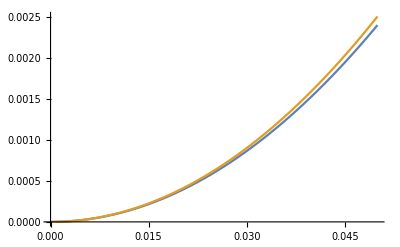

```mathematica
Plot[{numTrials/.{ηp1->0.8,ηp2->0.8,θ->1},averagePhotonNum[λ^2]/2},{λ,0,0.05}]
```

#### Simplified model

Just assume that can have only a 11 state or vacuum at input

```mathematica
probsFrom11={1/2 Sin[θ]^2((1-ηp1)^2+(1-ηp2)^2)+Cos[θ]^2(1-ηp1)(1-ηp2),Sin[θ]^2 ηp2(1-ηp2)+Cos[θ]^2 ηp2(1-ηp1),1/2 Sin[θ]^2 ηp2^2,Sin[θ]^2 ηp1(1-ηp1)+Cos[θ]^2 ηp1(1-ηp2),Cos[θ]^2 ηp1 ηp2,0,1/2 Sin[θ]^2 ηp1^2,0,0};
```

```mathematica
probsClickFrom11={1/2 Sin[θ]^2((1-ηp1)^2+(1-ηp2)^2)+Cos[θ]^2(1-ηp1)(1-ηp2),Sin[θ]^2 ηp2(1-ηp2)+Cos[θ]^2 ηp2(1-ηp1)+1/2 Sin[θ]^2 ηp2^2,Sin[θ]^2 ηp1(1-ηp1)+Cos[θ]^2 ηp1(1-ηp2)+1/2 Sin[θ]^2 ηp1^2,Cos[θ]^2 ηp1 ηp2};

probsFromNooN=λ^2 probsFrom11+(1-λ^2){1,0,0,0,0,0,0,0,0};
probsClickFromNooN=λ^2 probsClickFrom11+(1-λ^2){1,0,0,0};
```

#### Scaling of FI and QFI with squeezing parameter

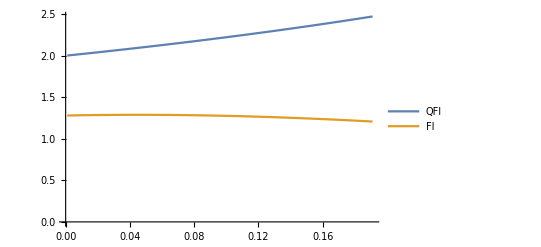

```mathematica
scaleDat=Transpose[Table[{{λSq,QFI[λSq,1]/averagePhotonNum[λSq]},{λSq,NMaxValue[Re[FIDist/.{ηp1->0.8,ηp2->0.8,λ->√λSq,ηd->1,pd->0}],θ]/averagePhotonNum[λSq]}},{λSq,0.001,0.2,0.01}]];ListPlot[scaleDat,PlotRange->{Automatic,{0,Automatic}},Joined->True,PlotLegends->{"QFI","FI"}]
```

### Expected performance

Lets start by assuming these parameters

```mathematica
λExpm=0.01;
η1Expm=0.78;
η2Expm=0.78;
ηdExpm=0.99;
pdExpm=0.000001;
```

#### Outcome probabilities

Here are the different outcomes for a click detector

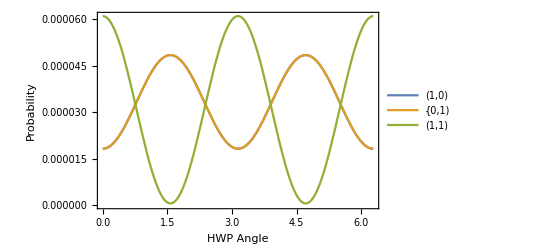

```mathematica
fullClickResults=Plot[Evaluate@Re[probNonNumberRes[[2;;]]/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm, pd->pdExpm}],{θ,0,2π},Frame->True,PlotLegends->{"(1,0)","{0,1)","(1,1)"},PlotRange->{Automatic,{0,Automatic}},FrameLabel->{"HWP Angle","Probability"}]
```

Comparison with simplified model

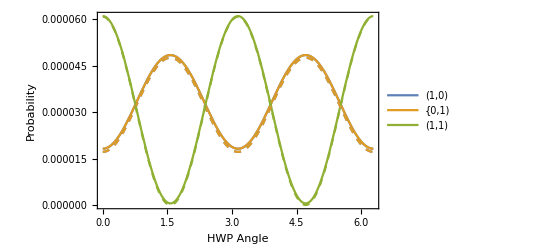

```mathematica
NooNClickResults=Plot[Evaluate@Re[probsClickFromNooN[[2;;]]/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm, pd->pdExpm}],{θ,0,2π},Frame->True,PlotStyle->Dashed,PlotRange->{Automatic,{0,Automatic}},FrameLabel->{"HWP Angle","Probability"}];
Show[{fullClickResults,NooNClickResults}]
```

Different outcomes for a PNR detector

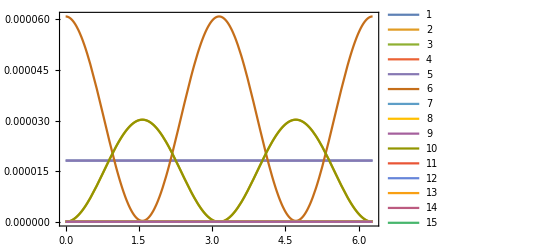

```mathematica
fullResults=Plot[Evaluate@Re[probsSimpDist[[2;;]]/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm,pd->pdExpm}],{θ,0,2π},Frame->True,PlotLegends->Automatic,PlotRange->All]
```

Comparison with simplified model

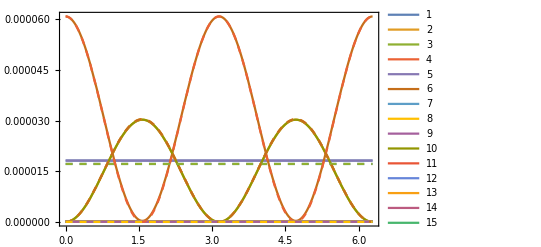

```mathematica
NooNresults=Plot[Evaluate@Re[probsFromNooN[[2;;]]/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm,pd->pdExpm}],{θ,0,2π},Frame->True,PlotStyle->Dashed,PlotRange->All];
Show[{fullResults,NooNresults}]
```

#### Classical Fisher Information

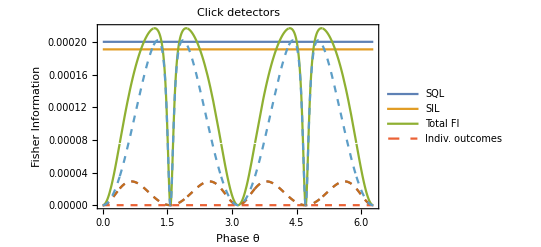

```mathematica
Plot[Evaluate@Re[Join@{averagePhotonNum[λ^2],2 numTrials,FINN,FINNProbByProb}/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm,pd->pdExpm}],{θ,0,2π},PlotRange->All,Frame->True,PlotLegends->{"SQL","SIL","Total FI","Indiv. outcomes"},PlotStyle->Join[{Automatic,Automatic,Automatic},ConstantArray[Dashed,4]],FrameLabel->{"Phase θ","Fisher Information"},PlotLabel->"Click detectors"]
```

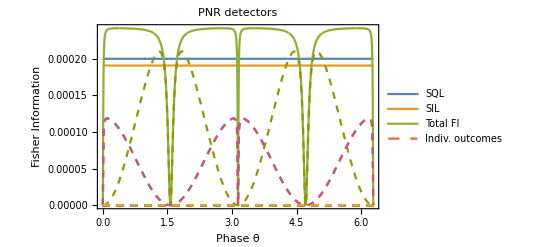

```mathematica
Plot[Evaluate@Re[Join@{averagePhotonNum[λ^2],2 numTrials,FIDist,FIDistProbByProb}/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm,pd->pdExpm}],{θ,0,2π},PlotRange->All,Frame->True,PlotLegends->{"SQL","SIL","Total FI","Indiv. outcomes"},PlotStyle->Join[{Automatic,Automatic,Automatic},ConstantArray[Dashed,matrixDim^2]],FrameLabel->{"Phase θ","Fisher Information"},PlotLabel->"PNR detectors"]
```

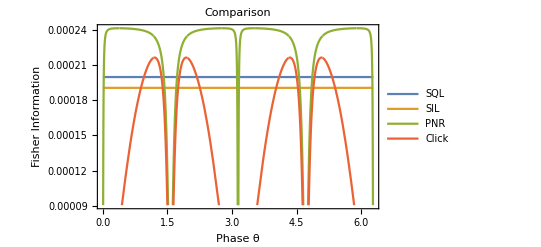

```mathematica
Plot[Evaluate@Re[Join@{averagePhotonNum[λ^2],2 numTrials,FIDist,FINN}/.{λ->λExpm,ηp1->η1Expm,ηp2->η2Expm,ηd->ηdExpm,pd->pdExpm}],{θ,0,2π},Frame->True,PlotLegends->{"SQL","SIL","PNR","Click"},FrameLabel->{"Phase θ","Fisher Information"},PlotLabel->"Comparison",PlotRange->{Automatic,Automatic}]
```

### Compare to experimental data

Here we load in the actual data

```mathematica
datadir="/Users/phumphreys/Dropbox/Set3/"
```

/Users/phumphreys/Dropbox/Set3/

```mathematica
files=FileNames["*HWP*",datadir];
data=Import[#]&/@files;
```

Additional data parameters

```mathematica
laserRep=3.64*^6;
rowInt=0.2;
```

Pull relevant values

```mathematica
hwp=#[[1,4]]&/@data;
order=Ordering[hwp];
hwp=hwp[[order]];
odata=data[[order]];
counts=#[[;;,1;;3]]&/@odata;
outcomes=Transpose@{#[[;;,1]]-#[[;;,3]],#[[;;,2]]-#[[;;,3]],#[[;;,3]]}&/@counts;
probs=#/(laserRep*rowInt)&/@outcomes;
meanProbs=Mean[#]&/@probs; (* P01,P10,P11 *)
meanCounts=Mean[#]&/@counts; (* Singles, coincidences *)
stdProbs=StandardDeviation[#]&/@probs;
combMean=(Transpose@{hwp,#}&/@Transpose[meanProbs]);
combMeanCounts=(Transpose@{hwp,#}&/@Transpose[meanCounts]);
```

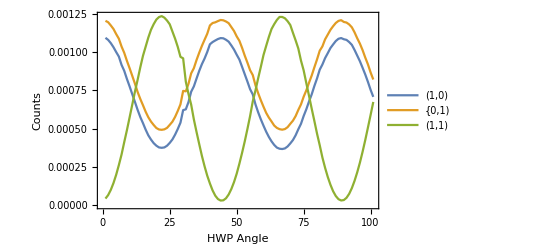

```mathematica
ListPlot[combMean,Joined->True,FrameLabel->{"HWP Angle","Counts"},PlotLegends->{"(1,0)","{0,1)","(1,1)"},Frame->True]
```

#### Fit model to expm

```mathematica
flatData=Flatten[Table[{i,hwp[[j]],meanProbs[[j,i]]},{i,1,3},{j,1,Dimensions[meanProbs][[1]]}],1];
```

```mathematica
expmModel= probNonNumberRes[[2;;]]/.θ->(4θ π/180-π/2+δθ);
combModel=Abs[Sum[Boole[i==j]expmModel[[j]] ,{j,1,3}]]; (* Want to fit all the data at once *)
```

```mathematica
nlm=NonlinearModelFit[flatData,{Evaluate[combModel/.{pd->0,ηd->0.98}],ηp1>0,ηp1<1,ηp2>0,ηp2<1,λ>0,λ<0.02,δθ<20,δθ>-20},{ηp1,ηp2,λ,δθ},{i,θ}];
```

```mathematica
nlm["BestFitParameters"]
```

(ηp1→0.703954
ηp2→0.699341
λ→0.0170836
δθ→0.0731524)

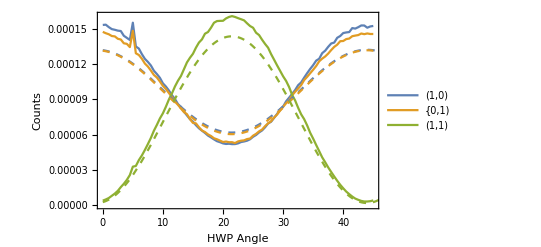

```mathematica
dp=ListPlot[combMean,Joined->True,FrameLabel->{"HWP Angle","Counts"},PlotLegends->{"(1,0)","{0,1)","(1,1)"},Frame->True];
mp=Plot[Evaluate[(expmModel/.{pd->0,ηd->0.98})/.nlm["BestFitParameters"]],{θ,0,100},FrameLabel->{"HWP Angle","Counts"},Frame->True,PlotStyle->Dashed];
Show[{dp,mp}]
```

#### Simpler approach, just fit the oscillations to get the amplitude, etc.

```mathematica
model=A (1-V Sin[(4 π θ)/180 +δθ]^2);
fits=Table[NonlinearModelFit[combMeanCounts[[i]],{model,V>0,A>0},{A,V,δθ},θ],{i,1,3}];
funcs=Table[model/.fits[[i]]["BestFitParameters"],{i,1,3}];
params=Table[{A,V}/.fits[[i]]["BestFitParameters"],{i,1,3}];
```

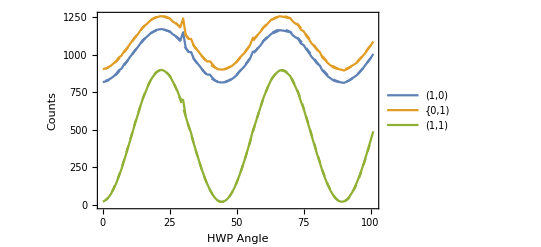

```mathematica
dp=ListPlot[combMeanCounts,Joined->True,FrameLabel->{"HWP Angle","Counts"},PlotLegends->{"(1,0)","{0,1)","(1,1)"},Frame->True];
mp=Plot[funcs,{θ,0,100},PlotRange->All,PlotStyle->Dashed];
Show[{dp,mp}]
```

Compare these oscillations with what would expect from our simple model.

```mathematica
FullSimplify[probsClickFromNooN]
```

(1/4 (4+(-4+ηp1+ηp2) (ηp1+ηp2) λ^2-(ηp1-ηp2)^2 λ^2 Cos[2 θ])
1/4 ηp2 λ^2 (4-2 ηp1-ηp2+(-2 ηp1+ηp2) Cos[2 θ])
1/4 ηp1 λ^2 (4-ηp1-2 ηp2+(ηp1-2 ηp2) Cos[2 θ])
ηp1 ηp2 λ^2 Cos[θ]^2)

```mathematica
pSing1=ηp1 λ^2 (1-1/2 ηp1 Sin[θ]^2)
pSing2=ηp2 λ^2 (1-1/2 ηp2 Sin[θ]^2)
pCoinc=ηp1 ηp2 λ^2 Cos[θ]^2
```

ηp1 λ^2 (1-1/2 ηp1 Sin[θ]^2)

ηp2 λ^2 (1-1/2 ηp2 Sin[θ]^2)

ηp1 ηp2 λ^2 Cos[θ]^2

```mathematica
η1Expm=2 params[[1,2]]
η2Expm=2 params[[2,2]]
```

If the data matched the model, these values should be the same (expected amplitude of coincidence probability oscillation):

```mathematica
Sqrt[4params[[1,1]]params[[1,2]]params[[2,1]]params[[2,2]]]
params[[3,1]]
```

704.609

898.795

They arent though..

Have a bash at trying to find a “best” solution

```mathematica
soln=NMinimize[{Abs[1/2 ηp1^2 A-params[[1,1]]params[[1,2]]]^2+Abs[1/2 ηp2^2 A-params[[2,1]]params[[2,2]]]^2+Abs[ηp1 ηp2 A-params[[3,1]]]^2,ηp1>0,ηp1<1,ηp2>0,ηp2<1,A>0},{ηp1 ,ηp2 ,A}][[2]]
```

(ηp1→0.877287
ηp2→0.880536
A→1079.72)

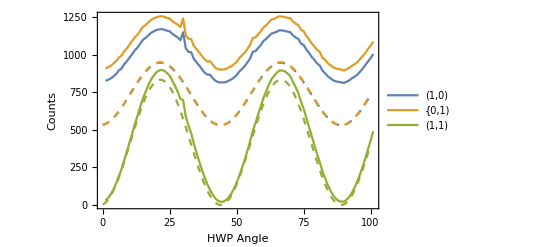

```mathematica
dp=ListPlot[combMeanCounts,Joined->True,FrameLabel->{"HWP Angle","Counts"},PlotLegends->{"(1,0)","{0,1)","(1,1)"},Frame->True];
mp=Plot[Evaluate[{pSing1,pSing2,pCoinc}/.{λ^2 ->A,θ->(4π (θt-21.5))/180}/.soln],{θt,0,100},PlotRange->All,PlotStyle->Dashed];
Show[{dp,mp}]
```